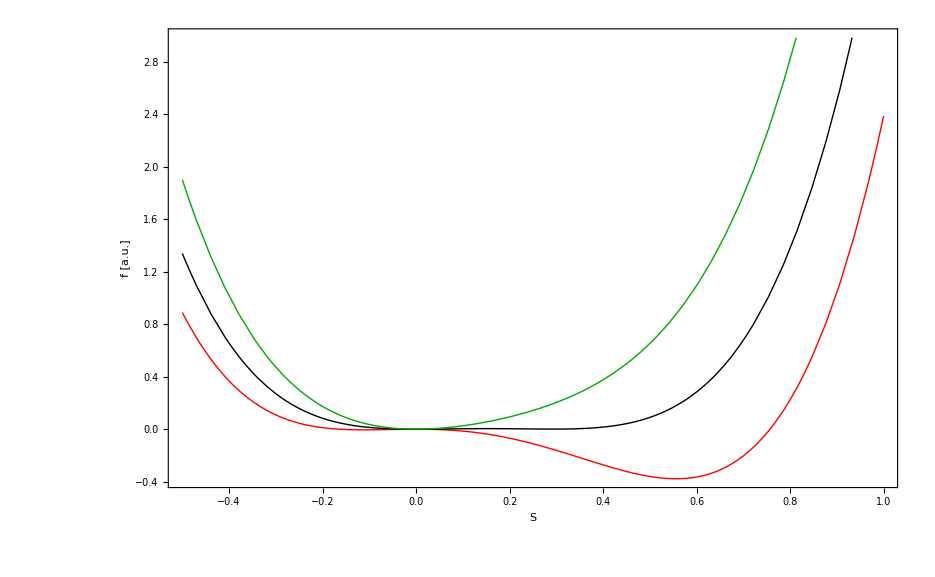

```mathematica
A = 0.2;
B =- 20;
c = 15;
T1=10;
f[S_,T_]:= 3/4 A(T-T1)S^2+1/4 B*S^3+9/16 c*S^4;
Plot[{f[S,3],f[S,T1+5],f[S,T1+20]},{S,-0.5,1},PlotRange->Automatic,Frame->True,FrameLabel->{"S","f [a.u.]"},LabelStyle->{Black,20},ImageSize->Large,AxesOrigin->{0,0},PlotStyle->{{Red,Thick},{Black,Thick},{Darker[Green],Thick}}]
```

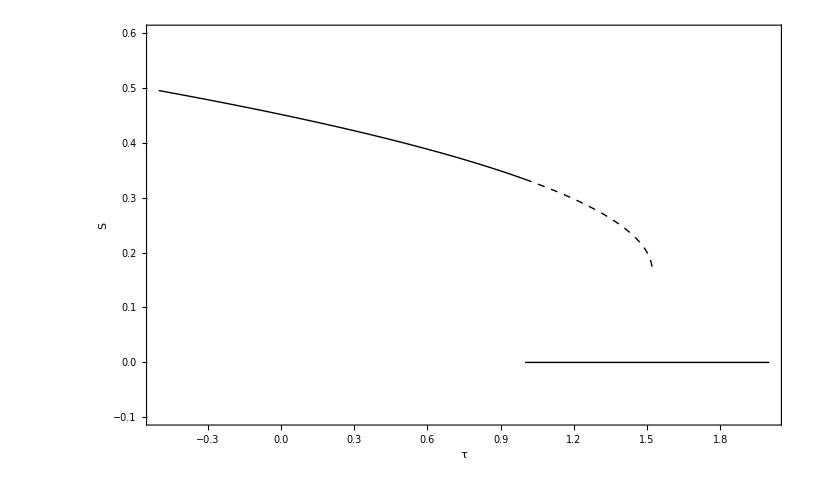

```mathematica
A = 0.4;
B =- 5;
c = 5;
T1=1;
S [T_]:=1/2(-B/(3c)+Sqrt[(B/(3c))^2-(8A(T-T1))/(3c)])
Show[Plot[S[T],{T,-0.5,1},PlotRange->{All,{-0.1,0.6}},Frame->True,FrameLabel->{"τ","S"},LabelStyle->{Black,20},ImageSize->Large,AxesOrigin->{0,0},PlotStyle->{{Black,Thick},{Black,Thick},{Darker[Green],Thick}}],Plot[{S[T],0},{T,1,2},PlotStyle->{{Black,Dashed,Thick}, {Black,Thick}}],Axes->False]
```